```mathematica
<<Local`SrednickiInit`
```

e1410: IntegralOp[{{F[n_]}},a__]:>IntegralOp[xF[n],a (n-1)! DiracDelta[∑_(i=1)^n x[i]-1]]

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1426: Gamma[-n+x]:>((-1)^n (1/x-γ+∑_(k=1)^n 1/k))/(n!)

#### 9.2) Consider a real scalar ﬁeld with L = L0 + L1 , where L0 = − 1/2 ∂µ ϕ ∂µ ϕ − 1/ 2 m 2 ϕ 2, L1 = − 1/24 Zλ λ ϕ 4 + Lct , Lct = − 1/2 (Zϕ−1)∂µ ϕ ∂µ ϕ − 1/2 (Zm−1)m 2 ϕ 2 .a) What kind of vertex appears in the diagrams for this theory (that is, how many line segments does it join?), and what is the associated vertex factor? b) Ignoring the counterterms, draw all the connected diagrams with 1 ≤ E ≤ 4 and 0 ≤ V ≤ 2, and ﬁnd their symmetry factors. c) Explain why we did not have to include a counterterm linear in ϕ to cancel tadpoles.

We follow the solution for the previous problem.

```mathematica
Clear[i,j,n,ii];DefPrint["p92",ℒ->-1/2 PartialD[φ[x[n,i]],μ]PartialD[φ[x[n,j]],ν]guu[μ,ν]
-1/2 m^2 φ[x[n,i]]φ[x[n,i]]
-1/24 Subscript[Z, λ] λ φ[x[n,i]]φ[x[n,i]]φ[x[n,i]]φ[x[n,i]]]
DefPrint["e96",Z->Exp[I IntegralOp[{{x[n,i]}},Subscript[ℒ, 1][1/I δOp[J[x[n,i]]]]]].Subscript[Z, 0]]
DefPrint["e97",Subscript[Z, 0]->Exp[I/2 IntegralOp[{{x[a,i]},{x[b,i]}},J[x[a,i]]. Δ[x[a,i]-x[b,i]].J[x[b,i]]]]]
DefPrint["e99",Subscript[ℒ, 1][φ_]->-1/24 Subscript[Z, λ].λ.φ.φ.φ.φ]
t96=e96/.e99/.SuperDagger[δOp[a_]]->δOp[SuperDagger[a]]/.SuperDagger[J[a_]]->SuperDagger[J][a]
```

p92: ℒ→-1/2 (φ[x_ni^ni])_(,μ) (φ[x_nj^nj])_(,ν) g_μν^μν-1/2 m^2 φ[x_ni^ni]^2-1/24 λ Z_λ φ[x_ni^ni]^4

e96: Z→ⅇ^(ⅈ IntegralOp[{{x_ni^ni}},ℒ_1[-ⅈ δOp[J[x_ni^ni]]]]).Z_0

e97: Z_0→ⅇ^(1/2 ⅈ IntegralOp[{{x_ai^ai},{x_bi^bi}},J[x_ai^ai].Δ[x_ai^ai-x_bi^bi].J[x_bi^bi]])

e99: ℒ_1[φ_]→-1/24 Z_λ.λ.φ.φ.φ.φ

Z→ⅇ^(ⅈ IntegralOp[{{x_ni^ni}},-1/24 Z_λ.λ.(-ⅈ δOp[J[x_ni^ni]]).(-ⅈ δOp[J[x_ni^ni]]).(-ⅈ δOp[J[x_ni^ni]]).(-ⅈ δOp[J[x_ni^ni]])]).Z_0

```mathematica
Clear[i,j,n,ii];
ordered={IntegralOp[_,_],δOp[_],J[_],SuperDagger[J][_],Δ[_],Subscript[Z, λ],λ};
nV=2;
nP=5;
t96=t96/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nV}]]//.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n]//UniqueIntVars(*Z*);
t97=e97/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nP}]]/.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n]//UniqueIntVars (*Z0*);
tmp=t96/.t97//UniqueIntVars;
tmp=dotRetain[ordered,tmp];
tmp[[2]]=tmp[[2]]//.IntDotInt2Int//.subIntInt2Int//dotRetain[ordered,#]&;
(***)
tmpSave=tmp
Length[tmpSave[[2]]]
```

Z→1+ⅈ IntegralOp[{{x_(106i)^(106i)}},-1/24 Z_λ.λ.δOp[J[x_(106i)^(106i)]].δOp[J[x_(106i)^(106i)]].δOp[J[x_(106i)^(106i)]].δOp[J[x_(106i)^(106i)]]]-1/2 IntegralOp[{{x_(41i)^(41i)},{x_(42i)^(42i)}},1/576 Z_λ.λ.δOp[J[x_(41i)^(41i)]].δOp[J[x_(41i)^(41i)]].δOp[J[x_(41i)^(41i)]].δOp[J[x_(41i)^(41i)]].Z_λ.λ.δOp[J[x_(42i)^(42i)]].δOp[J[x_(42i)^(42i)]].δOp[J[x_(42i)^(42i)]].δOp[J[x_(42i)^(42i)]]]+1/2 ⅈ IntegralOp[{{x_(107i)^(107i)},{x_(108i)^(108i)}},J[x_(107i)^(107i)].Δ[x_(107i)^(107i)-x_(108i)^(108i)].J[x_(108i)^(108i)]]-1/2 IntegralOp[{{x_(75i)^(75i)},{x_(76i)^(76i)},{x_(77i)^(77i)}},-1/24 Z_λ.λ.δOp[J[x_(75i)^(75i)]].δOp[J[x_(75i)^(75i)]].δOp[J[x_(75i)^(75i)]].δOp[J[x_(75i)^(75i)]].J[x_(76i)^(76i)].Δ[x_(76i)^(76i)-x_(77i)^(77i)].J[x_(77i)^(77i)]]-1/4 ⅈ IntegralOp[{{x_(37i)^(37i)},{x_(38i)^(38i)},{x_(39i)^(39i)},{x_(40i)^(40i)}},1/576 Z_λ.λ.δOp[J[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].δOp[J[x_(37i)^(37i)]].Z_λ.λ.δOp[J[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].δOp[J[x_(38i)^(38i)]].J[x_(39i)^(39i)].Δ[x_(39i)^(39i)-x_(40i)^(40i)].J[x_(40i)^(40i)]]-1/8 IntegralOp[{{x_(78i)^(78i)},{x_(79i)^(79i)},{x_(80i)^(80i)},{x_(81i)^(81i)}},J[x_(78i)^(78i)].Δ[x_(78i)^(78i)-x_(79i)^(79i)].J[x_(79i)^(79i)].J[x_(80i)^(80i)].Δ[x_(80i)^(80i)-x_(81i)^(81i)].J[x_(81i)^(81i)]]-1/8 ⅈ IntegralOp[{{x_(43i)^(43i)},{x_(44i)^(44i)},{x_(45i)^(45i)},{x_(46i)^(46i)},{x_(47i)^(47i)}},-1/24 Z_λ.λ.δOp[J[x_(43i)^(43i)]].δOp[J[x_(43i)^(43i)]].δOp[J[x_(43i)^(43i)]].δOp[J[x_(43i)^(43i)]].J[x_(44i)^(44i)].Δ[x_(44i)^(44i)-x_(45i)^(45i)].J[x_(45i)^(45i)].J[x_(46i)^(46i)].Δ[x_(46i)^(46i)-x_(47i)^(47i)].J[x_(47i)^(47i)]]+1/16 IntegralOp[{{x_(1i)^(1i)},{x_(2i)^(2i)},{x_(3i)^(3i)},{x_(4i)^(4i)},{x_(5i)^(5i)},{x_(6i)^(6i)}},1/576 Z_λ.λ.δOp[J[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].δOp[J[x_(1i)^(1i)]].Z_λ.λ.δOp[J[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].δOp[J[x_(2i)^(2i)]].J[x_(3i)^(3i)].Δ[x_(3i)^(3i)-x_(4i)^(4i)].J[x_(4i)^(4i)].J[x_(5i)^(5i)].Δ[x_(5i)^(5i)-x_(6i)^(6i)].J[x_(6i)^(6i)]]-1/48 ⅈ IntegralOp[{{x_(82i)^(82i)},{x_(83i)^(83i)},{x_(84i)^(84i)},{x_(85i)^(85i)},{x_(86i)^(86i)},{x_(87i)^(87i)}},J[x_(82i)^(82i)].Δ[x_(82i)^(82i)-x_(83i)^(83i)].J[x_(83i)^(83i)].J[x_(84i)^(84i)].Δ[x_(84i)^(84i)-x_(85i)^(85i)].J[x_(85i)^(85i)].J[x_(86i)^(86i)].Δ[x_(86i)^(86i)-x_(87i)^(87i)].J[x_(87i)^(87i)]]+1/48 IntegralOp[{{x_(48i)^(48i)},{x_(49i)^(49i)},{x_(50i)^(50i)},{x_(51i)^(51i)},{x_(52i)^(52i)},{x_(53i)^(53i)},{x_(54i)^(54i)}},-1/24 Z_λ.λ.δOp[J[x_(48i)^(48i)]].δOp[J[x_(48i)^(48i)]].δOp[J[x_(48i)^(48i)]].δOp[J[x_(48i)^(48i)]].J[x_(49i)^(49i)].Δ[x_(49i)^(49i)-x_(50i)^(50i)].J[x_(50i)^(50i)].J[x_(51i)^(51i)].Δ[x_(51i)^(51i)-x_(52i)^(52i)].J[x_(52i)^(52i)].J[x_(53i)^(53i)].Δ[x_(53i)^(53i)-x_(54i)^(54i)].J[x_(54i)^(54i)]]+1/96 ⅈ IntegralOp[{{x_(7i)^(7i)},{x_(8i)^(8i)},{x_(9i)^(9i)},{x_(10i)^(10i)},{x_(11i)^(11i)},{x_(12i)^(12i)},{x_(13i)^(13i)},{x_(14i)^(14i)}},1/576 Z_λ.λ.δOp[J[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].δOp[J[x_(7i)^(7i)]].Z_λ.λ.δOp[J[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].δOp[J[x_(8i)^(8i)]].J[x_(9i)^(9i)].Δ[x_(9i)^(9i)-x_(10i)^(10i)].J[x_(10i)^(10i)].J[x_(11i)^(11i)].Δ[x_(11i)^(11i)-x_(12i)^(12i)].J[x_(12i)^(12i)].J[x_(13i)^(13i)].Δ[x_(13i)^(13i)-x_(14i)^(14i)].J[x_(14i)^(14i)]]+1/384 IntegralOp[{{x_(88i)^(88i)},{x_(89i)^(89i)},{x_(90i)^(90i)},{x_(91i)^(91i)},{x_(92i)^(92i)},{x_(93i)^(93i)},{x_(94i)^(94i)},{x_(95i)^(95i)}},J[x_(88i)^(88i)].Δ[x_(88i)^(88i)-x_(89i)^(89i)].J[x_(89i)^(89i)].J[x_(90i)^(90i)].Δ[x_(90i)^(90i)-x_(91i)^(91i)].J[x_(91i)^(91i)].J[x_(92i)^(92i)].Δ[x_(92i)^(92i)-x_(93i)^(93i)].J[x_(93i)^(93i)].J[x_(94i)^(94i)].Δ[x_(94i)^(94i)-x_(95i)^(95i)].J[x_(95i)^(95i)]]+1/384 ⅈ IntegralOp[{{x_(55i)^(55i)},{x_(56i)^(56i)},{x_(57i)^(57i)},{x_(58i)^(58i)},{x_(59i)^(59i)},{x_(60i)^(60i)},{x_(61i)^(61i)},{x_(62i)^(62i)},{x_(63i)^(63i)}},-1/24 Z_λ.λ.δOp[J[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].δOp[J[x_(55i)^(55i)]].J[x_(56i)^(56i)].Δ[x_(56i)^(56i)-x_(57i)^(57i)].J[x_(57i)^(57i)].J[x_(58i)^(58i)].Δ[x_(58i)^(58i)-x_(59i)^(59i)].J[x_(59i)^(59i)].J[x_(60i)^(60i)].Δ[x_(60i)^(60i)-x_(61i)^(61i)].J[x_(61i)^(61i)].J[x_(62i)^(62i)].Δ[x_(62i)^(62i)-x_(63i)^(63i)].J[x_(63i)^(63i)]]-1/768 IntegralOp[{{x_(15i)^(15i)},{x_(16i)^(16i)},{x_(17i)^(17i)},{x_(18i)^(18i)},{x_(19i)^(19i)},{x_(20i)^(20i)},{x_(21i)^(21i)},{x_(22i)^(22i)},{x_(23i)^(23i)},{x_(24i)^(24i)}},1/576 Z_λ.λ.δOp[J[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].δOp[J[x_(15i)^(15i)]].Z_λ.λ.δOp[J[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].δOp[J[x_(16i)^(16i)]].J[x_(17i)^(17i)].Δ[x_(17i)^(17i)-x_(18i)^(18i)].J[x_(18i)^(18i)].J[x_(19i)^(19i)].Δ[x_(19i)^(19i)-x_(20i)^(20i)].J[x_(20i)^(20i)].J[x_(21i)^(21i)].Δ[x_(21i)^(21i)-x_(22i)^(22i)].J[x_(22i)^(22i)].J[x_(23i)^(23i)].Δ[x_(23i)^(23i)-x_(24i)^(24i)].J[x_(24i)^(24i)]]+1/3840 ⅈ IntegralOp[{{x_(96i)^(96i)},{x_(97i)^(97i)},{x_(98i)^(98i)},{x_(99i)^(99i)},{x_(100i)^(100i)},{x_(101i)^(101i)},{x_(102i)^(102i)},{x_(103i)^(103i)},{x_(104i)^(104i)},{x_(105i)^(105i)}},J[x_(96i)^(96i)].Δ[x_(96i)^(96i)-x_(97i)^(97i)].J[x_(97i)^(97i)].J[x_(98i)^(98i)].Δ[x_(98i)^(98i)-x_(99i)^(99i)].J[x_(99i)^(99i)].J[x_(100i)^(100i)].Δ[x_(100i)^(100i)-x_(101i)^(101i)].J[x_(101i)^(101i)].J[x_(102i)^(102i)].Δ[x_(102i)^(102i)-x_(103i)^(103i)].J[x_(103i)^(103i)].J[x_(104i)^(104i)].Δ[x_(104i)^(104i)-x_(105i)^(105i)].J[x_(105i)^(105i)]]-1/3840 IntegralOp[{{x_(64i)^(64i)},{x_(65i)^(65i)},{x_(66i)^(66i)},{x_(67i)^(67i)},{x_(68i)^(68i)},{x_(69i)^(69i)},{x_(70i)^(70i)},{x_(71i)^(71i)},{x_(72i)^(72i)},{x_(73i)^(73i)},{x_(74i)^(74i)}},-1/24 Z_λ.λ.δOp[J[x_(64i)^(64i)]].δOp[J[x_(64i)^(64i)]].δOp[J[x_(64i)^(64i)]].δOp[J[x_(64i)^(64i)]].J[x_(65i)^(65i)].Δ[x_(65i)^(65i)-x_(66i)^(66i)].J[x_(66i)^(66i)].J[x_(67i)^(67i)].Δ[x_(67i)^(67i)-x_(68i)^(68i)].J[x_(68i)^(68i)].J[x_(69i)^(69i)].Δ[x_(69i)^(69i)-x_(70i)^(70i)].J[x_(70i)^(70i)].J[x_(71i)^(71i)].Δ[x_(71i)^(71i)-x_(72i)^(72i)].J[x_(72i)^(72i)].J[x_(73i)^(73i)].Δ[x_(73i)^(73i)-x_(74i)^(74i)].J[x_(74i)^(74i)]]-1/7680 ⅈ IntegralOp[{{x_(25i)^(25i)},{x_(26i)^(26i)},{x_(27i)^(27i)},{x_(28i)^(28i)},{x_(29i)^(29i)},{x_(30i)^(30i)},{x_(31i)^(31i)},{x_(32i)^(32i)},{x_(33i)^(33i)},{x_(34i)^(34i)},{x_(35i)^(35i)},{x_(36i)^(36i)}},1/576 Z_λ.λ.δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].Z_λ.λ.δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].J[x_(27i)^(27i)].Δ[x_(27i)^(27i)-x_(28i)^(28i)].J[x_(28i)^(28i)].J[x_(29i)^(29i)].Δ[x_(29i)^(29i)-x_(30i)^(30i)].J[x_(30i)^(30i)].J[x_(31i)^(31i)].Δ[x_(31i)^(31i)-x_(32i)^(32i)].J[x_(32i)^(32i)].J[x_(33i)^(33i)].Δ[x_(33i)^(33i)-x_(34i)^(34i)].J[x_(34i)^(34i)].J[x_(35i)^(35i)].Δ[x_(35i)^(35i)-x_(36i)^(36i)].J[x_(36i)^(36i)]]

18

```mathematica
"Find propagator correction term (2P-4V==2)."
Clear[i,j,n,ii];
tmpl=Apply[List,tmpSave[[2]]];
For[Clear[ii];ii=1,ii≤Length[tmpl],ii++,
tmp=Extract[tmpl[[ii]],Position[tmpl[[ii]],IntegralOp[__]]][[1,2]];
tmp=Apply[List,tmp]/.Dot->List//Flatten;
If[
Count[tmp,δOp[_]]-
Count[tmp,J[_]]==-2&&Count[tmp,λ]==2,Print[tmp1=tmpSave[[2,ii]]]
];
]
```

Find propagator correction term (2P-4V==2).

Part::partw: Part 1 of {} does not exist.

-1/7680 ⅈ IntegralOp[{{x_(25i)^(25i)},{x_(26i)^(26i)},{x_(27i)^(27i)},{x_(28i)^(28i)},{x_(29i)^(29i)},{x_(30i)^(30i)},{x_(31i)^(31i)},{x_(32i)^(32i)},{x_(33i)^(33i)},{x_(34i)^(34i)},{x_(35i)^(35i)},{x_(36i)^(36i)}},1/576 Z_λ.λ.δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].δOp[J[x_(25i)^(25i)]].Z_λ.λ.δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].δOp[J[x_(26i)^(26i)]].J[x_(27i)^(27i)].Δ[x_(27i)^(27i)-x_(28i)^(28i)].J[x_(28i)^(28i)].J[x_(29i)^(29i)].Δ[x_(29i)^(29i)-x_(30i)^(30i)].J[x_(30i)^(30i)].J[x_(31i)^(31i)].Δ[x_(31i)^(31i)-x_(32i)^(32i)].J[x_(32i)^(32i)].J[x_(33i)^(33i)].Δ[x_(33i)^(33i)-x_(34i)^(34i)].J[x_(34i)^(34i)].J[x_(35i)^(35i)].Δ[x_(35i)^(35i)-x_(36i)^(36i)].J[x_(36i)^(36i)]]

```mathematica
Clear[i,j,n,ii];
tmp1=OpδIntegrand[tmp1]/.cleanInt;
tmp1>>"saveSrednicki.9.2.tmp1"
tmp2=findEvalIntDelta[tmp1];
tmp2>>"saveSrednicki.9.2.tmp2"
M1
tmp3=UniformIntVar1[tmp2];
tmp3>>"saveSrednicki.9.2.tmp3"
M2
tmp4=tmp3/.Null->0/.Dot->Times//Expand;
tmp4>>"saveSrednicki.9.2.tmp4"
M3
tmp5=gatherIntFast[tmp4];
tmp5>>"saveSrednicki.9.2.tmp5"
tmp6=tmp5/.Δ[-x[a_,i]+x[b_,i]]->Δd[M[a]M[b] ]/.Δd[M[a_] M[b_]]->Δ[x[a,i]- x[b,i]]
(*sign of argument of Δ not important*)
MM
tmp6>>"saveSrednicki.9.2.tmp6"
tmp7=RearrangeIntJArg[tmp6]
```

M1

M2

M3

IntegralOp[{{x_(d[1]i)^(d[1]i)},{x_(d[2]i)^(d[2]i)},{x_(d[3]i)^(d[3]i)},{x_(d[4]i)^(d[4]i)}},-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]-1/960 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2-(ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)])/1280-1/160 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/48 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-7/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4]

MM

IntegralOp[{{x_(d[1]i)^(d[1]i)},{x_(d[2]i)^(d[2]i)},{x_(d[3]i)^(d[3]i)},{x_(d[4]i)^(d[4]i)}},-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]-1/960 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2-(ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)])/1280-1/160 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/48 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-7/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4]

```mathematica
tmp7>>"saveSrednicki.9.2.tmp7"
tmp8=GroupJΔ[tmp7]
tmp8>>"saveSrednicki.9.2.tmp8"
```

IntegralOp:1:-1/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]-1/960 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2-1/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2-(ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)])/1280-1/160 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[3]i)^(d[3]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/240 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/48 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[4]i)^(d[4]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/480 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/320 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^3 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/32 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-1/160 ⅈ λ^2 J[x_(d[2]i)^(d[2]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-3/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/480 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[3]i)^(d[3]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3 Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]-7/320 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0]^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-7/160 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[0] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/40 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)] Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3-1/120 ⅈ λ^2 J[x_(d[1]i)^(d[1]i)] J[x_(d[2]i)^(d[2]i)] Z_λ^2 Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)] Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4

term:1 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]}
-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^4

term:2 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]}
-1/960 ⅈ λ^2 Z_λ^2 Δ[0]^4

term:3 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]}
-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:4 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]}
-1/120 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:5 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]}
{Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2}
-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:6 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]}
-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:7 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:8 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:9 groups:{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-(ⅈ λ^2 Z_λ^2 Δ[0]^4)/1280

term:10 groups:{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:11 groups:{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4}
-1/480 ⅈ λ^2 Z_λ^2

term:12 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:13 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:14 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/480 ⅈ λ^2 Z_λ^2

term:15 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:16 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/48 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:17 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2,Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:18 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-3/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:19 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-7/480 ⅈ λ^2 Z_λ^2

term:20 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:21 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:22 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:23 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/480 ⅈ λ^2 Z_λ^2

term:24 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

term:25 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:26 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/40 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:27 groups:{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2,Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:28 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-3/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:29 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]}
-7/480 ⅈ λ^2 Z_λ^2

term:30 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]}
{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2}
-7/320 ⅈ λ^2 Z_λ^2 Δ[0]^2

term:31 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2}
-7/160 ⅈ λ^2 Z_λ^2 Δ[0]

term:32 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2}
-1/40 ⅈ λ^2 Z_λ^2 Δ[0]

term:33 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3}
-1/40 ⅈ λ^2 Z_λ^2

term:34 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3}
-1/40 ⅈ λ^2 Z_λ^2

term:35 groups:{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]}
{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4}
-1/120 ⅈ λ^2 Z_λ^2

{{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]},-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^4},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]},-1/960 ⅈ λ^2 Z_λ^2 Δ[0]^4},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]},-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]},-1/120 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]},{Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2},-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]},-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-(ⅈ λ^2 Z_λ^2 Δ[0]^4)/1280},{{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^2},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[3]i)^(d[3]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},{Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]^4},-1/480 ⅈ λ^2 Z_λ^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/480 ⅈ λ^2 Z_λ^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/48 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)]^2,Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^2,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-3/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-7/480 ⅈ λ^2 Z_λ^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/480 ⅈ λ^2 Z_λ^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/40 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)]^2,Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-1/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^2,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-3/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)]^3,Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]},-7/480 ⅈ λ^2 Z_λ^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]},{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2},-7/320 ⅈ λ^2 Z_λ^2 Δ[0]^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2},-7/160 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^2},-1/40 ⅈ λ^2 Z_λ^2 Δ[0]},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3},-1/40 ⅈ λ^2 Z_λ^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[3]i)^(d[3]i)],Δ[x_(d[2]i)^(d[2]i)-x_(d[4]i)^(d[4]i)],Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^3},-1/40 ⅈ λ^2 Z_λ^2},{{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)],Δ[x_(d[1]i)^(d[1]i)-x_(d[2]i)^(d[2]i)]},{Δ[x_(d[3]i)^(d[3]i)-x_(d[4]i)^(d[4]i)]^4},-1/120 ⅈ λ^2 Z_λ^2}}

35

------1:2-----Coefficient:-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^4

------2:2-----Coefficient:-1/960 ⅈ λ^2 Z_λ^2 Δ[0]^4

------3:2-----Coefficient:-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

------4:2-----Coefficient:-1/120 ⅈ λ^2 Z_λ^2 Δ[0]^3

------6:2-----Coefficient:-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

------7:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

------8:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

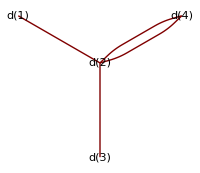
{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)]}:{d[1]→d[2],d[2]→d[3],d[2]→d[4],d[2]→d[4]}:
-Graphics-

------9:2-----Coefficient:-(ⅈ λ^2 Z_λ^2 Δ[0]^4)/1280

------12:2-----Coefficient:-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^3

------13:2-----Coefficient:-1/240 ⅈ λ^2 Z_λ^2 Δ[0]^2

------14:2-----Coefficient:-1/480 ⅈ λ^2 Z_λ^2

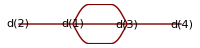
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)]}:{d[1]→d[2],d[1]→d[3],d[1]→d[3],d[1]→d[3],d[3]→d[4]}:
-Graphics-

------15:2-----Coefficient:-1/480 ⅈ λ^2 Z_λ^2 Δ[0]^3

------16:2-----Coefficient:-1/48 ⅈ λ^2 Z_λ^2 Δ[0]^2

------17:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

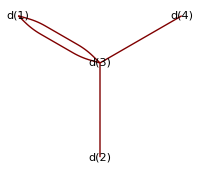
{J[x_(d[2]i)^(d[2]i)],J[x_(d[4]i)^(d[4]i)]}:{d[1]→d[3],d[1]→d[3],d[2]→d[3],d[3]→d[4]}:
-Graphics-

------18:2-----Coefficient:-3/160 ⅈ λ^2 Z_λ^2 Δ[0]

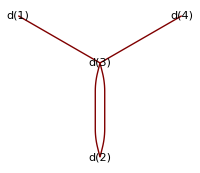
{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)]}:{d[1]→d[3],d[2]→d[3],d[2]→d[3],d[3]→d[4]}:
-Graphics-

------19:2-----Coefficient:-7/480 ⅈ λ^2 Z_λ^2

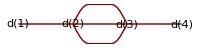
{J[x_(d[1]i)^(d[1]i)],J[x_(d[4]i)^(d[4]i)]}:{d[1]→d[2],d[2]→d[3],d[2]→d[3],d[2]→d[3],d[3]→d[4]}:
-Graphics-

------20:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^3

------21:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]^2

------22:2-----Coefficient:-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2

------23:2-----Coefficient:-1/480 ⅈ λ^2 Z_λ^2

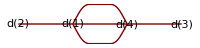
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)]}:{d[1]→d[2],d[1]→d[4],d[1]→d[4],d[1]→d[4],d[3]→d[4]}:
-Graphics-

------24:2-----Coefficient:-1/320 ⅈ λ^2 Z_λ^2 Δ[0]^3

------25:2-----Coefficient:-1/32 ⅈ λ^2 Z_λ^2 Δ[0]^2

------26:2-----Coefficient:-1/40 ⅈ λ^2 Z_λ^2 Δ[0]^2

------27:2-----Coefficient:-1/160 ⅈ λ^2 Z_λ^2 Δ[0]

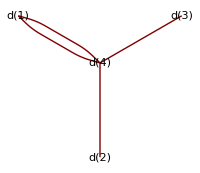
{J[x_(d[2]i)^(d[2]i)],J[x_(d[3]i)^(d[3]i)]}:{d[1]→d[4],d[1]→d[4],d[2]→d[4],d[3]→d[4]}:
-Graphics-

------28:2-----Coefficient:-3/160 ⅈ λ^2 Z_λ^2 Δ[0]

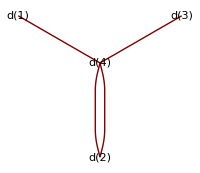
{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)]}:{d[1]→d[4],d[2]→d[4],d[2]→d[4],d[3]→d[4]}:
-Graphics-

------29:2-----Coefficient:-7/480 ⅈ λ^2 Z_λ^2

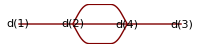
{J[x_(d[1]i)^(d[1]i)],J[x_(d[3]i)^(d[3]i)]}:{d[1]→d[2],d[2]→d[4],d[2]→d[4],d[2]→d[4],d[3]→d[4]}:
-Graphics-

------31:2-----Coefficient:-7/160 ⅈ λ^2 Z_λ^2 Δ[0]

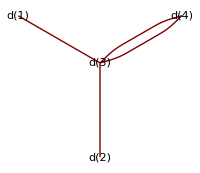
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)]}:{d[1]→d[3],d[2]→d[3],d[3]→d[4],d[3]→d[4]}:
-Graphics-

------32:2-----Coefficient:-1/40 ⅈ λ^2 Z_λ^2 Δ[0]

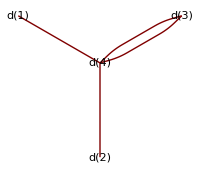
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)]}:{d[1]→d[4],d[2]→d[4],d[3]→d[4],d[3]→d[4]}:
-Graphics-

------33:2-----Coefficient:-1/40 ⅈ λ^2 Z_λ^2

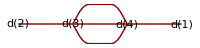
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)]}:{d[2]→d[3],d[1]→d[4],d[3]→d[4],d[3]→d[4],d[3]→d[4]}:
-Graphics-

------34:2-----Coefficient:-1/40 ⅈ λ^2 Z_λ^2

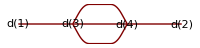
{J[x_(d[1]i)^(d[1]i)],J[x_(d[2]i)^(d[2]i)]}:{d[1]→d[3],d[2]→d[4],d[3]→d[4],d[3]→d[4],d[3]→d[4]}:
-Graphics-

The coefficient Δ[0] represents a loop and its configuration depends upon the other parts of the graph.  A single Δ[0] is a single loop attached at a node point.

```mathematica
tmp8//Length
PlotΔ[tmp8,2,3]
"The coefficient Δ[0] represents a loop and its configuration depends upon the other parts of the graph.  A single Δ[0] is a single loop attached at a node point."
```